## Setup

#### Docked cell

```mathematica
CurrentValue[EvaluationNotebook[],DockedCells]={};
```

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/nikm/DeveloperDockedCell"]["Wolfram`Cotengra`",
FileNameJoin[{NotebookDirectory[],"..","Cotengra"}]]
```

## Playground

```mathematica
?Wolfram`Cotengra`*
```

```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
qc=;
```

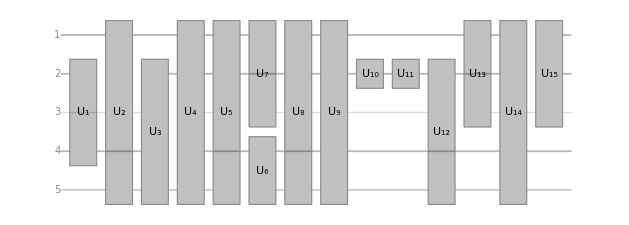

```mathematica
qc["Diagram"]
```

```mathematica
net=qc["TensorNetwork"];
tnData=TensorNetworkData@net;
```

```mathematica
t1=ActivateTensor@EinsteinSummation[tnData["ContractionIndices"],tnData["Tensors"]];
```

```mathematica
path=TensorNetworkContractionPath[net,"Optimal"->True]
```

{{18},{15},{12},{9},{16},{14},{12},{10},{8},{11},{10},{9},{8},{8,17},{1,19},{11,12},{1,15},{7,16},{9,12},{2,6},{8,13},{9,12},{10,11},{3,10},{6,9},{7,8},{4,7},{3,6},{3,5},{2,4},{2,3},{1,2}}

```mathematica
CanonicalPath[path]
```

{{18,19},{1,19},{1,9},{9,17},{8,9},{11,8},{2,8},{7,13},{11,12},{10,11},{3,10},{4,9},{7,8},{4,7},{3,6},{3,5},{2,4},{2,3},{1,2}}

Grouped contraction indices following the path order:

```mathematica
PathIndexContractions[CanonicalPath[path],tnData["Contractions"]]
```

{{{13^1,14_1},{13^3,14_3}},{{5^1,7_1}},{{6^5,8_5}},{{9^3,12_3},{9^5,12_5}},{{10^2,11_2}},{{9^2,10_2},{11^2,12_2}},{{6^4,9_4},{8^1,9_1},{8^2,9_2},{8^3,9_3},{8^5,9_5}},{{(-1)^4,1_4}},{{1^4,3_4}},{{(-3)^2,1_2},{5^2,8_2},{7^3,8_3}},{{3^2,4_2},{3^5,4_5},{4^1,5_1},{4^2,5_2},{4^3,5_3},{4^4,6_4},{4^5,5_5}},{{2^1,4_1},{2^3,3_3},{2^5,3_5}},{{0^5,2_5}},{{(-4)^1,2_1},{9^1,13_1},{9^4,14_4},{12^2,14_2},{12^5,14_5},{14^3,15_3}},{{(-2)^3,2_3}}}

Grouped global contraction indices:

```mathematica
PathIndexContractions[CanonicalPath[path],tnData["Indices"],tnData["Contractions"]]
```

{{{65,71},{66,73}},{{28,38}},{{35,45}},{{48,63},{50,64}},{{56,59}},{{47,57},{58,62}},{{34,54},{39,51},{40,52},{41,53},{42,55}},{{4,8}},{{6,18}},{{2,7},{29,43},{37,44}},{{15,26},{16,27},{20,30},{21,31},{22,32},{23,36},{24,33}},{{9,25},{10,17},{11,19}},{{5,14}},{{1,12},{46,67},{49,74},{60,72},{61,75},{68,79}},{{3,13}}}

Flat list of contraction index pairs for TensorContract:

```mathematica
pathContraction=PathIndexContractions[CanonicalPath[path],tnData]
```

{{65,71},{66,73},{28,38},{35,45},{48,63},{50,64},{56,59},{47,57},{58,62},{34,54},{39,51},{40,52},{41,53},{42,55},{4,8},{6,18},{2,7},{29,43},{37,44},{15,26},{16,27},{20,30},{21,31},{22,32},{23,36},{24,33},{9,25},{10,17},{11,19},{5,14},{1,12},{46,67},{49,74},{60,72},{61,75},{68,79},{3,13}}

```mathematica
t2=First@TensorContract[Inactive[TensorProduct]@@tnData["Tensors"],pathContraction]
```

SparseArray[…]

```mathematica
Chop[t1-t2,1*^-7]
```

SparseArray[…]

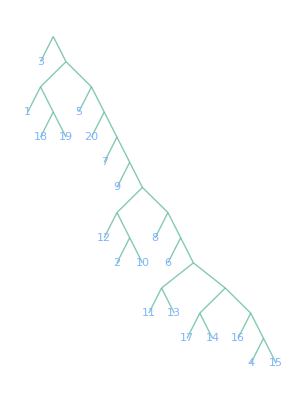

```mathematica
ExpressionTree[PathToTreePath[path] /. {{x_} :> x,List->Null}]
```